### Start choosing the example:

```mathematica
t=27;
beta = 1;
A = 0.2;
V[x]
g[x]
```

0.2 Sin[2 π (1/4+x)]^2

Log[x]

```mathematica
beta
```

1

```mathematica
IntM[65]
```

-1.79148×10^106

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Intg[65]
```

-1.79148×10^106

```mathematica
Data["Entrance Vertices and Currents"]={{1,65}};
Data["Exit Vertices and Terminal Costs"]={{10,0}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.023461,Null}

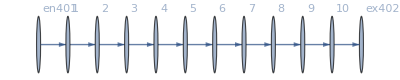

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j403→65.,j404→65.,j405→65.,j406→65.,j407→65.,j408→65.,j409→65.,j410→65.,j411→65.,j412→65.,j413→65.,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65.,jt427→65.,jt428→0.,jt429→65.,jt430→0.,jt431→65.,jt432→0.,jt433→65.,jt434→0.,jt435→65.,jt436→0.,jt437→65.,jt438→0.,jt439→65.,jt440→0.,jt441→65.,jt442→0.,jt443→65.,jt444→0.,u445→585.,u446→520.,u447→455.,u448→390.,u449→325.,u450→260.,u451→195.,u452→130.,u453→65.,u454→0.,u455→585.,u456→520.,u457→455.,u458→390.,u459→325.,u460→260.,u461→195.,u462→130.,u463→65.,u464→0.,u465→0.,u466→585.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.13201×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.13201×10^-17

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→22.6018,u446→20.0905,u447→17.5792,u448→15.0679,u449→12.5565,u450→10.0452,u451→7.53393,u452→5.02262,u453→2.51131,u454→0.,u455→22.6018,u456→20.0905,u457→17.5792,u458→15.0679,u459→12.5565,u460→10.0452,u461→7.53393,u462→5.02262,u463→2.51131,u464→0,u465→0.,u466→22.6018|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.29024×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.29024×10^-16

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→27.4093,u446→24.3639,u447→21.3184,u448→18.2729,u449→15.2274,u450→12.1819,u451→9.13645,u452→6.09096,u453→3.04548,u454→0.,u455→27.4093,u456→24.3639,u457→21.3184,u458→18.2729,u459→15.2274,u460→12.1819,u461→9.13645,u462→6.09096,u463→3.04548,u464→0,u465→0.,u466→27.4093|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.42115×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.42115×10^-17

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→42.5885,u446→37.8565,u447→33.1244,u448→28.3924,u449→23.6603,u450→18.9282,u451→14.1962,u452→9.46412,u453→4.73206,u454→0.,u455→42.5885,u456→37.8565,u457→33.1244,u458→28.3924,u459→23.6603,u460→18.9282,u461→14.1962,u462→9.46412,u463→4.73206,u464→0,u465→0.,u466→42.5885|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.14923×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.14923×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→339.64,u446→301.902,u447→264.165,u448→226.427,u449→188.689,u450→150.951,u451→113.213,u452→75.4756,u453→37.7378,u454→0.,u455→339.64,u456→301.902,u457→264.165,u458→226.427,u459→188.689,u460→150.951,u461→113.213,u462→75.4756,u463→37.7378,u464→0,u465→0.,u466→339.64|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.13163×10^-13

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→585.,u446→520.,u447→455.,u448→390.,u449→325.,u450→260.,u451→195.,u452→130.,u453→65.,u454→0.,u455→585.,u456→520.,u457→455.,u458→390.,u459→325.,u460→260.,u461→195.,u462→130.,u463→65.,u464→0,u465→0.,u466→585.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22884×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22884×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→2435.55,u446→2164.93,u447→1894.32,u448→1623.7,u449→1353.08,u450→1082.47,u451→811.85,u452→541.233,u453→270.617,u454→0.,u455→2435.55,u456→2164.93,u457→1894.32,u458→1623.7,u459→1353.08,u460→1082.47,u461→811.85,u462→541.233,u463→270.617,u464→0,u465→0.,u466→2435.55|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.15348×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.15348×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→117620.,u446→104551.,u447→91482.1,u448→78413.2,u449→65344.4,u450→52275.5,u451→39206.6,u452→26137.7,u453→13068.9,u454→0.,u455→117620.,u456→104551.,u457→91482.1,u458→78413.2,u459→65344.4,u460→52275.5,u461→39206.6,u462→26137.7,u463→13068.9,u464→0,u465→0.,u466→117620.|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.68093×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.68093×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→1.2569×10^6,u446→1.11725×10^6,u447→977592.,u448→837936.,u449→698280.,u450→558624.,u451→418968.,u452→279312.,u453→139656.,u454→0.,u455→1.2569×10^6,u456→1.11725×10^6,u457→977592.,u458→837936.,u459→698280.,u460→558624.,u461→418968.,u462→279312.,u463→139656.,u464→0,u465→0.,u466→1.2569×10^6|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.24736×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.24736×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→1.26053×10^6,u446→1.12047×10^6,u447→980414.,u448→840355.,u449→700295.,u450→560236.,u451→420177.,u452→280118.,u453→140059.,u454→0.,u455→1.26053×10^6,u456→1.12047×10^6,u457→980414.,u458→840355.,u459→700295.,u460→560236.,u461→420177.,u462→280118.,u463→140059.,u464→0,u465→0.,u466→1.26053×10^6|>

```mathematica
alpha = 1.605;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.48616×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.48616×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→1.45398×10^6,u446→1.29242×10^6,u447→1.13087×10^6,u448→969317.,u449→807764.,u450→646211.,u451→484658.,u452→323106.,u453→161553.,u454→0.,u455→1.45398×10^6,u456→1.29242×10^6,u457→1.13087×10^6,u458→969317.,u459→807764.,u460→646211.,u461→484658.,u462→323106.,u463→161553.,u464→0,u465→0.,u466→1.45398×10^6|>

```mathematica
alpha = 1.61;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.46491×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.46491×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→1.68744×10^6,u446→1.49994×10^6,u447→1.31245×10^6,u448→1.12496×10^6,u449→937464.,u450→749971.,u451→562478.,u452→374986.,u453→187493.,u454→0.,u455→1.68744×10^6,u456→1.49994×10^6,u457→1.31245×10^6,u458→1.12496×10^6,u459→937464.,u460→749971.,u461→562478.,u462→374986.,u463→187493.,u464→0,u465→0.,u466→1.68744×10^6|>

```mathematica
alpha = 1.62;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.40891×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.40891×10^-16

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→2.29625×10^6,u446→2.04111×10^6,u447→1.78597×10^6,u448→1.53083×10^6,u449→1.27569×10^6,u450→1.02055×10^6,u451→765416.,u452→510277.,u453→255139.,u454→0.,u455→2.29625×10^6,u456→2.04111×10^6,u457→1.78597×10^6,u458→1.53083×10^6,u459→1.27569×10^6,u460→1.02055×10^6,u461→765416.,u462→510277.,u463→255139.,u464→0,u465→0.,u466→2.29625×10^6|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.55884×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.55884×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→6.34142×10^6,u446→5.63681×10^6,u447→4.93221×10^6,u448→4.22761×10^6,u449→3.52301×10^6,u450→2.81841×10^6,u451→2.11381×10^6,u452→1.4092×10^6,u453→704602.,u454→0.,u455→6.34142×10^6,u456→5.63681×10^6,u457→4.93221×10^6,u458→4.22761×10^6,u459→3.52301×10^6,u460→2.81841×10^6,u461→2.11381×10^6,u462→1.4092×10^6,u463→704602.,u464→0,u465→0.,u466→6.34142×10^6|>

```mathematica
alpha = 1.7;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.3596×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.3596×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→5.08383×10^7,u446→4.51896×10^7,u447→3.95409×10^7,u448→3.38922×10^7,u449→2.82435×10^7,u450→2.25948×10^7,u451→1.69461×10^7,u452→1.12974×10^7,u453→5.6487×10^6,u454→0.,u455→5.08383×10^7,u456→4.51896×10^7,u457→3.95409×10^7,u458→3.38922×10^7,u459→2.82435×10^7,u460→2.25948×10^7,u461→1.69461×10^7,u462→1.12974×10^7,u463→5.6487×10^6,u464→0,u465→0.,u466→5.08383×10^7|>

```mathematica
alpha = 1.8;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54679×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54679×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54679×10^-15

«2 more identical outputs»

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→4.47371×10^10,u446→3.97663×10^10,u447→3.47955×10^10,u448→2.98247×10^10,u449→2.48539×10^10,u450→1.98831×10^10,u451→1.49124×10^10,u452→9.94157×10^9,u453→4.97079×10^9,u454→0.,u455→4.47371×10^10,u456→3.97663×10^10,u457→3.47955×10^10,u458→2.98247×10^10,u459→2.48539×10^10,u460→1.98831×10^10,u461→1.49124×10^10,u462→9.94157×10^9,u463→4.97079×10^9,u464→0,u465→0.,u466→4.47371×10^10|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→2.02187×10^18,u446→1.79722×10^18,u447→1.57257×10^18,u448→1.34792×10^18,u449→1.12326×10^18,u450→8.98611×10^17,u451→6.73958×10^17,u452→4.49305×10^17,u453→2.24653×10^17,u454→0.,u455→2.02187×10^18,u456→1.79722×10^18,u457→1.57257×10^18,u458→1.34792×10^18,u459→1.12326×10^18,u460→8.98611×10^17,u461→6.73958×10^17,u462→4.49305×10^17,u463→2.24653×10^17,u464→0,u465→0.,u466→2.02187×10^18|>

```mathematica
alpha = 1.91;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5,SameTest-> (Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.36953×10^-15

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.36953×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→7.15338×10^19,u446→6.35856×10^19,u447→5.56374×10^19,u448→4.76892×10^19,u449→3.9741×10^19,u450→3.17928×10^19,u451→2.38446×10^19,u452→1.58964×10^19,u453→7.9482×10^18,u454→0.,u455→7.15338×10^19,u456→6.35856×10^19,u457→5.56374×10^19,u458→4.76892×10^19,u459→3.9741×10^19,u460→3.17928×10^19,u461→2.38446×10^19,u462→1.58964×10^19,u463→7.9482×10^18,u464→0,u465→0.,u466→7.15338×10^19|>

```mathematica
alpha = 1.99;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5,SameTest-> (Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.51348×10^-15

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.51348×10^-15

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→1.61447×10^99,u446→1.43508×10^99,u447→1.2557×10^99,u448→1.07631×10^99,u449→8.96926×10^98,u450→7.17541×10^98,u451→5.38156×10^98,u452→3.58771×10^98,u453→1.79385×10^98,u454→0.,u455→1.61447×10^99,u456→1.43508×10^99,u457→1.2557×10^99,u458→1.07631×10^99,u459→8.96926×10^98,u460→7.17541×10^98,u461→5.38156×10^98,u462→3.58771×10^98,u463→1.79385×10^98,u464→0,u465→0.,u466→1.61447×10^99|>

```mathematica
alpha =2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],5,SameTest-> (Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.37651×10^-16

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.37651×10^-16

<|j403→65,j404→65,j405→65,j406→65,j407→65,j408→65,j409→65,j410→65,j411→65,j412→65,j413→65,j414→0.,j415→0.,j416→0.,j417→0.,j418→0.,j419→0.,j420→0.,j421→0.,j422→0.,j423→0.,j424→0.,jt425→0.,jt426→65,jt427→65,jt428→0.,jt429→65,jt430→0.,jt431→65,jt432→0.,jt433→65,jt434→0.,jt435→65,jt436→0.,jt437→65,jt438→0.,jt439→65,jt440→0.,jt441→65,jt442→0.,jt443→65,jt444→0.,u445→1.61233×10^107,u446→1.43318×10^107,u447→1.25404×10^107,u448→1.07489×10^107,u449→8.9574×10^106,u450→7.16592×10^106,u451→5.37444×10^106,u452→3.58296×10^106,u453→1.79148×10^106,u454→0.,u455→1.61233×10^107,u456→1.43318×10^107,u457→1.25404×10^107,u458→1.07489×10^107,u459→8.9574×10^106,u460→7.16592×10^106,u461→5.37444×10^106,u462→3.58296×10^106,u463→1.79148×10^106,u464→0,u465→0.,u466→1.61233×10^107|>

```mathematica
aux = <|j2603->65,u2655->0.,j2593->65,j2594->65,j2595->65,j2596->65,j2597->65,j2598->65,j2599->65,j2600->65,j2601->65,j2602->65,j2604->0.,j2605->0.,j2606->0.,j2607->0.,j2608->0.,j2609->0.,j2610->0.,j2611->0.,j2612->0.,j2613->0.,j2614->0.,jt2615->0.,jt2616->65,jt2617->65,jt2618->0.,jt2619->65,jt2620->0.,jt2621->65,jt2622->0.,jt2623->65,jt2624->0.,jt2625->65,jt2626->0.,jt2627->65,jt2628->0.,jt2629->65,jt2630->0.,jt2631->65,jt2632->0.,jt2633->65,jt2634->0.,u2644->0.,u2656->0.+1. (0.+1. 7.153383732831773*^19),u2645->0.+1. 7.153383732831773*^19,u2646->6.358563318072687*^19,u2647->5.5637429033136005*^19,u2648->4.768922488554515*^19,u2649->3.974102073795428*^19,u2650->3.1792816590363427*^19,u2651->2.384461244277257*^19,u2652->1.5896408295181713*^19,u2653->7.948204147590857*^18,u2654->0,u2635->7.153383732831773*^19,u2636->6.358563318072687*^19,u2637->5.5637429033136005*^19,u2638->4.768922488554515*^19,u2639->3.974102073795428*^19,u2640->3.1792816590363427*^19,u2641->2.384461244277257*^19,u2642->1.5896408295181713*^19,u2643->7.948204147590857*^18|>;
```

```mathematica
MFGEquations["Nlhs"]/MFGEquations["Nrhs"]
MFGEquations["Nlhs"]/.aux

MFGEquations["Nrhs"]/.aux
(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nrhs"]/.aux
```

{(j3051-j3062-u3093+u3104)/(j3051-j3062+IntM[j3051-j3062]),(j3052-j3063-u3094+u3105)/(j3052-j3063+IntM[j3052-j3063]),(j3053-j3064-u3095+u3106)/(j3053-j3064+IntM[j3053-j3064]),(j3054-j3065-u3096+u3107)/(j3054-j3065+IntM[j3054-j3065]),(j3055-j3066-u3097+u3108)/(j3055-j3066+IntM[j3055-j3066]),(j3056-j3067-u3098+u3109)/(j3056-j3067+IntM[j3056-j3067]),(j3057-j3068-u3099+u3110)/(j3057-j3068+IntM[j3057-j3068]),(j3058-j3069-u3100+u3111)/(j3058-j3069+IntM[j3058-j3069]),(j3059-j3070-u3101+u3112)/(j3059-j3070+IntM[j3059-j3070])}

{j3051-j3062-u3093+u3104,j3052-j3063-u3094+u3105,j3053-j3064-u3095+u3106,j3054-j3065-u3096+u3107,j3055-j3066-u3097+u3108,j3056-j3067-u3098+u3109,j3057-j3068-u3099+u3110,j3058-j3069-u3100+u3111,j3059-j3070-u3101+u3112}

{j3051-j3062+IntM[j3051-j3062],j3052-j3063+IntM[j3052-j3063],j3053-j3064+IntM[j3053-j3064],j3054-j3065+IntM[j3054-j3065],j3055-j3066+IntM[j3055-j3066],j3056-j3067+IntM[j3056-j3067],j3057-j3068+IntM[j3057-j3068],j3058-j3069+IntM[j3058-j3069],j3059-j3070+IntM[j3059-j3070]}

{(-u3093+u3104-IntM[j3051-j3062])/(j3051-j3062+IntM[j3051-j3062]),(-u3094+u3105-IntM[j3052-j3063])/(j3052-j3063+IntM[j3052-j3063]),(-u3095+u3106-IntM[j3053-j3064])/(j3053-j3064+IntM[j3053-j3064]),(-u3096+u3107-IntM[j3054-j3065])/(j3054-j3065+IntM[j3054-j3065]),(-u3097+u3108-IntM[j3055-j3066])/(j3055-j3066+IntM[j3055-j3066]),(-u3098+u3109-IntM[j3056-j3067])/(j3056-j3067+IntM[j3056-j3067]),(-u3099+u3110-IntM[j3057-j3068])/(j3057-j3068+IntM[j3057-j3068]),(-u3100+u3111-IntM[j3058-j3069])/(j3058-j3069+IntM[j3058-j3069]),(-u3101+u3112-IntM[j3059-j3070])/(j3059-j3070+IntM[j3059-j3070])}

### What we this plot for?

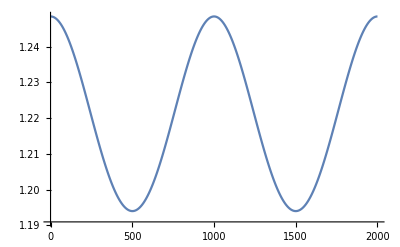

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.